```mathematica
Quit[]
```

```mathematica
defAssumError :=Element[α,Reals]&&α≥0&&α≤1&&Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[a,Reals]
distError := Assuming[defAssumError,MixtureDistribution[{α,1-α},{NormalDistribution[0,σ],UniformDistribution[{0,b}]}]]
denError[z_] = PDF[distError,e]
```

Piecewise[{{(1-α)/b+(ⅇ^(-e^2/(2 σ^2)) α)/(√(2 π) σ), e≥0&&b-e≥0}, {(ⅇ^(-e^2/(2 σ^2)) α)/(√(2 π) σ), True}}]

```mathematica
(*y=x+e, e~αN(0,σ^2)+1-αU(0,b)*)
distMix := TransformedDistribution[a+e,e\[Distributed]distError]
denMix[y_] = PDF[distMix,y]
cumMix[y_] = CDF[distMix,y]
```

Piecewise[{{(1-α)/b+(ⅇ^(-(-a+y)^2/(2 σ^2)) α)/(√(2 π) σ), a-y≤0&&a+b-y≥0}, {(ⅇ^(-(-a+y)^2/(2 σ^2)) α)/(√(2 π) σ), True}}]

Piecewise[{{1/2 α Erfc[(a-y)/(√2 σ)], a-y>0}, {((-a+y) (1-α))/b+1/2 α Erfc[(a-y)/(√2 σ)], a-y≤0&&a+b-y≥0}, {1-α+1/2 α Erfc[(a-y)/(√2 σ)], True}}]

```mathematica
(* order statistic*)
defAssumOrder :=Element[α,Reals]&&α≥0&&α≤1&&Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[a,Reals]&&Element[n,Integers]&&n>1&&Element[a,Reals]&&Element[y,Reals]
distOrder :=Simplify[OrderDistribution[{distMix,n},k],defAssumOrder]
denOrder[y_]=Simplify[PDF[distOrder,y],defAssumOrder]
```

Piecewise[{{(2^(-1/2+k-n) ⅇ^(-(a-y)^2/(2 σ^2)) k α Binomial[n,k] (1-α+1/2 α Erfc[(a-y)/(√2 σ)])^(-1+k) (α Erfc[(-a+y)/(√2 σ)])^(-k+n))/(√π σ), a+b<y}, {k ((1-α)/b+(ⅇ^(-(a-y)^2/(2 σ^2)) α)/(√(2 π) σ)) Binomial[n,k] (((a-y) (-1+α))/b+1/2 α Erfc[(a-y)/(√2 σ)])^(-1+k) (-((a+b-y) (-1+α))/b+1/2 α Erfc[(-a+y)/(√2 σ)])^(-k+n), a≤y&&a+b≥y}, {(2^(1/2-k) ⅇ^(-(a-y)^2/(2 σ^2)) k α Binomial[n,k] (α Erfc[(a-y)/(√2 σ)])^(-1+k) (1-α+1/2 α Erfc[(-a+y)/(√2 σ)])^(-k+n))/(√π σ), True}}]

```mathematica
(* minimum order statistic*)
defAssumMinOrder :=Element[α,Reals]&&α≥0&&α≤1&&Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[n,Integers]&&n>1&&Element[a,Reals]&&Element[y,Reals]
distMinOrder :=Simplify[OrderDistribution[{distMix,n},1],defAssumMinOrder]
denOrder[y_]=Simplify[PDF[distMinOrder,y],defAssumMinOrder]
```

Piecewise[{{(2^(1/2-n) ⅇ^(-(a-y)^2/(2 σ^2)) n α (α Erfc[(-a+y)/(√2 σ)])^(-1+n))/(√π σ), a+b<y}, {n ((1-α)/b+(ⅇ^(-(a-y)^2/(2 σ^2)) α)/(√(2 π) σ)) (-((a+b-y) (-1+α))/b+1/2 α Erfc[(-a+y)/(√2 σ)])^(-1+n), a≤y&&a+b≥y}, {(ⅇ^(-(a-y)^2/(2 σ^2)) n α (1-α+1/2 α Erfc[(-a+y)/(√2 σ)])^(-1+n))/(√(2 π) σ), True}}]

```mathematica
(*best order statistic*)
defAssumBestOrder :=Element[α,Reals]&&α≥0&&α≤1&&Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[n,Integers]&&n>0&&0≤(n*α/2)≤ n/2&&Element[a,Reals]&&Element[y,Reals]
distXhat :=Assuming[defAssumBestOrder,Simplify[OrderDistribution[{distMix,n},Ceiling[(n*α/2)]]]]
denXhat[y_]=Assuming[defAssumBestOrder,Simplify[PDF[distXhat,y]]]
NIntegrate[y*denXhat[y],{y,-Infinity,Infinity}]
```

Piecewise[{{(2^(1/2-n) ⅇ^(-(a-y)^2/(2 σ^2)) α Binomial[n,Ceiling[(n α)/2]] Ceiling[(n α)/2] (2-2 α+α Erfc[(a-y)/(√2 σ)])^(-1+Ceiling[(n α)/2]) (α Erfc[(-a+y)/(√2 σ)])^(n-Ceiling[(n α)/2]))/(√π σ), a+b<y}, {((1-α)/b+(ⅇ^(-(a-y)^2/(2 σ^2)) α)/(√(2 π) σ)) Binomial[n,Ceiling[(n α)/2]] Ceiling[(n α)/2] (((a-y) (-1+α))/b+1/2 α Erfc[(a-y)/(√2 σ)])^(-1+Ceiling[(n α)/2]) (-((a+b-y) (-1+α))/b+1/2 α Erfc[(-a+y)/(√2 σ)])^(n-Ceiling[(n α)/2]), a≤y&&a+b≥y}, {(2^(1/2-Ceiling[(n α)/2]) ⅇ^(-(a-y)^2/(2 σ^2)) α Binomial[n,Ceiling[(n α)/2]] Ceiling[(n α)/2] (α Erfc[(a-y)/(√2 σ)])^(-1+Ceiling[(n α)/2]) (1-α+1/2 α Erfc[(-a+y)/(√2 σ)])^(n-Ceiling[(n α)/2]))/(√π σ), True}}]

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate[y denXhat[y],{y,-∞,∞}]

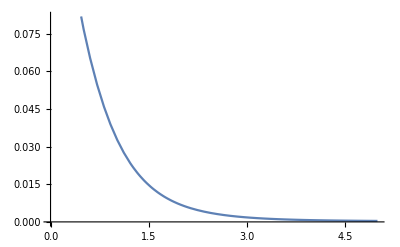

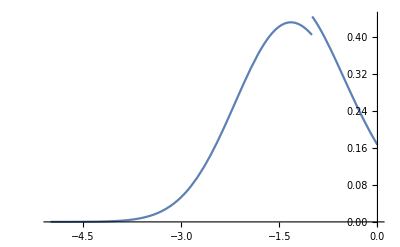

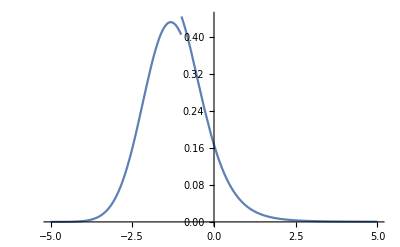

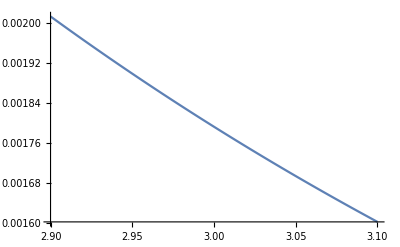

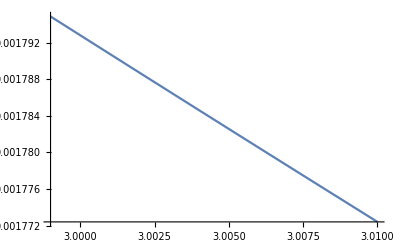

Piecewise[{{4.50033×10^-7 ⅇ^(-1/8 (-1-y)^2) (1.+0.5 Erfc[(-1-y)/(2 √2)])^4 Erfc[(1+y)/(2 √2)]^15, 49<y}, {77520 (0.01+0.0997356 ⅇ^(-1/8 (-1-y)^2)) (-0.01 (-1-y)+0.25 Erfc[(-1-y)/(2 √2)])^4 (0.01 (49-y)+0.25 Erfc[(1+y)/(2 √2)])^15, -1≤y&&49≥y}, {30.2012 ⅇ^(-1/8 (-1-y)^2) Erfc[(-1-y)/(2 √2)]^4 (0.5+0.25 Erfc[(1+y)/(2 √2)])^15, True}}]

0.108126

0.0785128

```mathematica
(*Plot to see how it looks*)
n:=20
α:=0.5
σ:= 2
b:=50
a:=-1
Plot[denXhat[y],{y,0,5}]
Plot[denXhat[y],{y,0,-5}]
Plot[denXhat[y],{y,-5,5}]
Plot[denXhat[y],{y,2.9,3.1}]
Plot[denXhat[y],{y,2.999,3.01}]
denXhat[y]
(*N[Integrate[denXhat[y],{y,2,4}]]*)
NIntegrate[denXhat[y],{y,0,Infinity}]
NIntegrate[y*denXhat[y],{y,0,Infinity}]
```

```mathematica
(*find bias and estimate*)
(*Assuming[defAssumBestOrder,Simplify[Integrate[y*denXhat[y],{y,0,Infinity}]]]*)
α:=0.5
n:=100
defAssumXhat :=Element[b,Reals]&&b>0&&Element[σ,Reals]&&σ>0&&Element[n,Integers]&&n>0&&0≤(n*α/2)≤ n/2&&Element[a,Reals]&&Element[y,Reals]&&a≤y
Assuming[defAssumXhat,Simplify[Expectation[y,y\[Distributed]distXhat]]]
```

Expectation[y,y\[Distributed]OrderDistribution[{TransformedDistribution[x+a,x\[Distributed]MixtureDistribution[{0.5,0.5},{NormalDistribution[0,σ],UniformDistribution[{0,b}]}]],100},25]]

```mathematica
Clear[α,n,b,σ,a]
```